```mathematica
(*Типовой расчет*)
(*гр.221703*)
(*Гаврилович Алиса*)
(*Вариант 3*)


func=({{-0.5, 0.535916}, {-0.42, 0.485126}, {-0.34, 0.437118}, {-0.26, 0.371678}, {-0.18, 0.301733}, {-0.1, 0.207338}, {-0.02, 0.073557}, {0.06, 0.155576}, {0.14, 0.283913}, {0.22, 0.390199}, {0.3, 0.497748}, {0.38, 0.592501}, {0.46, 0.69812}, {0.54, 0.789936}, {0.62, 0.898493}, {0.7, 0.990582}, {0.78, 1.10445}, {0.86, 1.19854}, {0.94, 1.31926}, {1.02, 1.4165}, {1.1, 1.54526}, {1.18, 1.64652}, {1.26, 1.78436}, {1.34, 1.89036}, {1.42, 2.03825}, {1.5, 2.14963}});
n=26;
a=-0.5;
b=1.5;
h=0.08;
```

0.235254+0.370954 x+1.66263 x^2-1.16062 x^3+0.302118 x^4

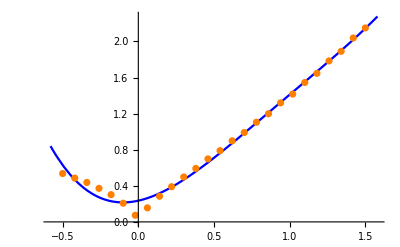

```mathematica
Q[x_]=Fit[func,{1,x,x^2,x^3,x^4},x]
gr=Plot[Q[x],{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[func,PlotStyle->Orange];
Show[gr,points]
```

```mathematica
(*Задание 1*)
(*пункт а*)
n=12;
h=0.08*2;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*2-1,2]]];
TableForm[data]
```

-0.5 | 0.535916
-0.34 | 0.437118
-0.18 | 0.301733
-0.02 | 0.073557
0.14 | 0.283913
0.3 | 0.497748
0.46 | 0.69812
0.62 | 0.898493
0.78 | 1.10445
0.94 | 1.31926
1.1 | 1.54526
1.26 | 1.78436
1.42 | 2.03825

0.0883836+0.900074 x+7.29475 x^2-31.9226 x^3+15.109 x^4+230.893 x^5-590.834 x^6+208.357 x^7+1283.89 x^8-2456.59 x^9+2017.52 x^10-815.908 x^11+132.599 x^12

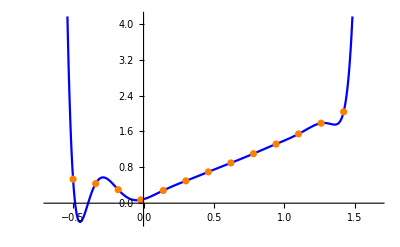

```mathematica
Np[x_]=InterpolatingPolynomial[data,x];(*интерполяционный многочлен Ньютона*)
Np[x_]=Expand[Np[x]]
gr=Plot[Np[x],{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

-0.5 | 0.535916
-0.26 | 0.371678
-0.02 | 0.073557
0.22 | 0.390199
0.46 | 0.69812
0.7 | 0.990582
0.94 | 1.31926
1.18 | 1.64652
1.42 | 2.03825

0.08849+0.847463 x+4.78533 x^2-12.7153 x^3+3.11932 x^4+32.7907 x^5-52.0479 x^6+31.3522 x^7-6.82225 x^8

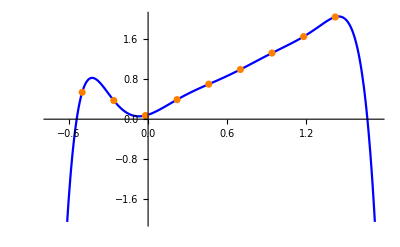

```mathematica
(*Пункт б*)
h=0.08*3;
n=8;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*3-2,2]]];
TableForm[data]
Np[x_]=InterpolatingPolynomial[data,x];
Np[x_]=Expand[Np[x]]
gr=Plot[Np[x],{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

```mathematica
(*пункт в*)
```

-0.5 | 0.535916
-0.1 | 0.207338
0.3 | 0.497748
0.7 | 0.990582
1.1 | 1.54526
1.5 | 2.14963

0.244286+0.523098 x+1.40213 x^2-1.27649 x^3+0.629315 x^4-0.120081 x^5

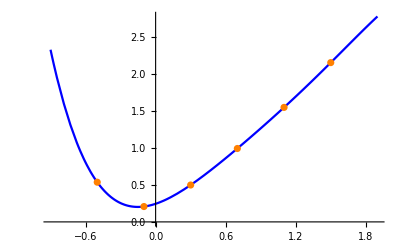

```mathematica
h=0.08*5;
n=5;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*5-4,2]]];
TableForm[data]
Np[x_]=InterpolatingPolynomial[data,x];
Np[x_]=Expand[Np[x]]
gr=Plot[Np[x],{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

```mathematica
(*Задание 2*)
```

```mathematica
(*пункт а*)
```

-0.5 | 0.535916
-0.34 | 0.437118
-0.18 | 0.301733
-0.02 | 0.073557
0.14 | 0.283913
0.3 | 0.497748
0.46 | 0.69812
0.62 | 0.898493
0.78 | 1.10445
0.94 | 1.31926
1.1 | 1.54526
1.26 | 1.78436
1.42 | 2.03825

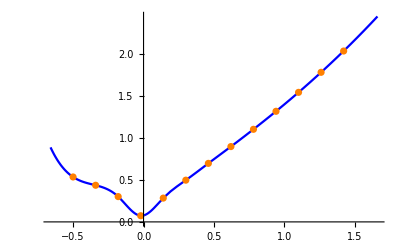

```mathematica
n=12;
h=0.08*2;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*2-1,2]]];
TableForm[data]
spl=Interpolation[data,Method->"Spline"];
gr=Plot[{spl[x]},{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

-0.5 | 0.535916
-0.26 | 0.371678
-0.02 | 0.073557
0.22 | 0.390199
0.46 | 0.69812
0.7 | 0.990582
0.94 | 1.31926
1.18 | 1.64652
1.42 | 2.03825

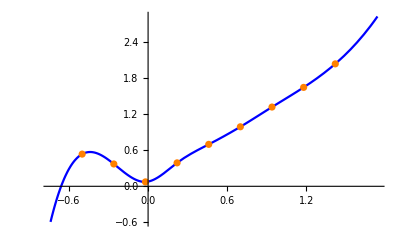

```mathematica
(*пункт б*)
h=0.08*3;
n=8;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*3-2,2]]];
TableForm[data]
spl=Interpolation[data,Method->"Spline"];
gr=Plot[{spl[x]},{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

```mathematica
(*пункт в*)
```

```mathematica
(*Вывод: с ростом количества узлов, погрешность интерполирования уменьшается*)
```

-0.5 | 0.535916
-0.1 | 0.207338
0.3 | 0.497748
0.7 | 0.990582
1.1 | 1.54526
1.5 | 2.14963

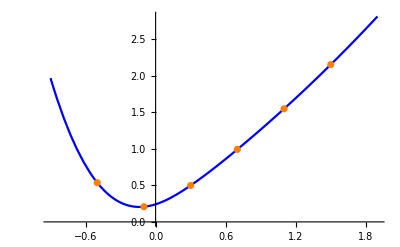

```mathematica
h=0.08*5;
n=5;
data=Table[{a+i*h,0},{i,0,n}];
For[i=0,i<=n,i++;
data[[i,2]]=func[[i*5-4,2]]];
TableForm[data]
spl=Interpolation[data,Method->"Spline"];
gr=Plot[{spl[x]},{x,a-h,b+h}, PlotStyle->Blue];
points=ListPlot[data,PlotStyle->Orange];
Show[gr,points]
```

```mathematica
(*Вывод: чем больше количество узлов,тем меньше погрешность интерполирования*)
(*Задание 3*)
```

```mathematica
n=26;
h=0.08;
data=Table[{a+i*h,0},{i,0,n-1}];
For[i=0,i<n,i++;
data[[i,2]]=func[[i,2]]];
Q[x_]=Fit[data,{1,x},x](*многочлен наилучшего cреднеквадратичного приближения степени 1*)
```

0.438312+0.954351 x

```mathematica
S=∑_(i=1)^n (Q[data[[i,1]]]-data[[i,2]])^2(*Квадратичное отклонение*)
```

1.46588

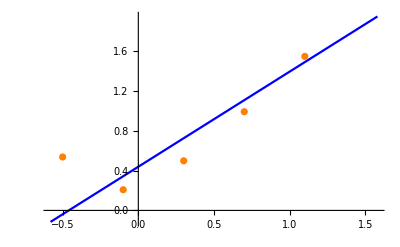

```mathematica
gr1=Plot[{Q[x]},{x,a-h,b+h}, PlotStyle->Blue];
Show[gr1,points]
```

```mathematica
Q[x_]=Fit[data,{1,x,x^2},x](*многочлен наилучшего cреднеквадратичного приближения степени 2*)
```

0.366463+0.301183 x+0.653168 x^2

```mathematica
S=∑_(i=1)^n (Q[data[[i,1]]]-data[[i,2]])^2(*Квадратичное отклонение *)
```

0.320933

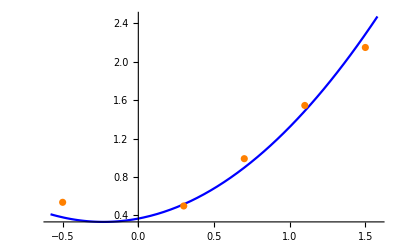

```mathematica
gr1=Plot[{Q[x]},{x,a-h,b+h}, PlotStyle->Blue];
Show[gr1,points]
```

```mathematica
(*Вывод:чем больше степень многочлена наилучшего cреднеквадратичного приближения,тем меньше погрешность приближения*)
```

```mathematica
(*Задание 4*)
n=25;
h=(b-a)/n;
k=2;
(*формула левых прямоугольников*)
int=h*∑_(i=1)^(n-1) data[[i,2]]
```

1.56918

```mathematica
(*формула правых прямоугольников*)
```

```mathematica
int=h*∑_(i=2)^n data[[i,2]]
```

1.68937

```mathematica
(*формула средних прямоугольников*)
```

```mathematica
int = h*∑_(i=1)^(n-1) (data[[i,2]]+data[[i+1,2]])/2
```

1.62928

```mathematica
(*формула трапеций*)
```

```mathematica
int=h*(∑_(i=2)^(n-1) data[[i,2]]+data[[1,2]]/2+data[[n,2]]/2)
```

1.62928

```mathematica
(*Формула Симпсона*)
```

```mathematica
n=12;
h=(b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
```

```mathematica
int=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

1.69449

```mathematica
(*Выведем значение интеграла апроксимированной функции для сравнения*)
```

```mathematica
Q=Fit[data,{1,x,x^2,x^3,x^4},x];
Integrate[Q,{x,a,b}]
```

1.79115

```mathematica
(*самыми точными для данной функции оказались метод Симпсона и формула правых прямоугольников*)
```

```mathematica
(*Задание 5*)
Clear[Q,Func,firstDerivative]
n=25;
h=(b-a)/n;
Q[x]=Fit[data,{1,x,x^2,x^3,x^4},x];
Func1[x_]=D[Q[x],x];
Func2[x_]=D[Q[x],{x,2}];
firstDerivative=N[Table[{data[[i,1]],Func1[data[[i,1]]]},{i,1,n}]];
secondDerivative=N[Table[{data[[i,1]],Func2[data[[i,1]]]},{i,1,n}]];
(*таблица первых производных первого порядка точности*)
pr11Table=N[Table[{(data[[i+1,2]]-data[[i,2]])/h},{i,1,n}]];
(*таблица первых производных второго порядка точности*)
pr12Table=N[Table[{(data[[i+1,2]]-data[[i-1,2]])/(2*h)},{i,2,n}]];
(*таблица вторых производных *)
pr2Table=N[Table[{(data[[i+1,2]]-2data[[i,2]]+data[[i-1,2]])/h^2},{i,2,n-1}]];

TableForm[pr11Table]
TableForm[pr12Table]
TableForm[pr2Table]
TableForm[firstDerivative]
TableForm[secondDerivative]
```

-0.634875
-0.6001
-0.818
-0.874313
-1.17994
-1.67226
1.02524
1.60421
1.32857
1.34436
1.18441
1.32024
1.1477
1.35696
1.15111
1.42335
1.17613
1.509
1.2155
1.6095
1.26575
1.723
1.325
1.84863
1.39225

-0.617487
-0.70905
-0.846156
-1.02713
-1.4261
-0.323513
1.31473
1.46639
1.33647
1.26439
1.25232
1.23397
1.25233
1.25404
1.28723
1.29974
1.34256
1.36225
1.4125
1.43762
1.49437
1.524
1.58681
1.62044

0.434687
-2.72375
-0.703906
-3.82031
-6.15406
33.7188
7.23719
-3.44547
0.197344
-1.99937
1.69781
-2.15672
2.61578
-2.57313
3.40297
-3.09031
4.16094
-3.66875
4.925
-4.29688
5.71563
-4.975
6.54531

-0.5 | -2.31321
-0.42 | -1.72939
-0.34 | -1.20964
-0.26 | -0.75023
-0.18 | -0.347454
-0.1 | 0.0024004
-0.02 | 0.303046
0.06 | 0.558196
0.14 | 0.771563
0.22 | 0.946858
0.3 | 1.08779
0.38 | 1.19808
0.46 | 1.28144
0.54 | 1.34157
0.62 | 1.3822
0.7 | 1.40703
0.78 | 1.41977
0.86 | 1.42415
0.94 | 1.42386
1.02 | 1.42263
1.1 | 1.42416
1.18 | 1.43217
1.26 | 1.45037
1.34 | 1.48247
1.42 | 1.53219

-0.5 | 7.71349
-0.42 | 6.88956
-0.34 | 6.11204
-0.26 | 5.38092
-0.18 | 4.6962
-0.1 | 4.05789
-0.02 | 3.46599
0.06 | 2.92049
0.14 | 2.4214
0.22 | 1.96871
0.3 | 1.56243
0.38 | 1.20255
0.46 | 0.889081
0.54 | 0.622015
0.62 | 0.401354
0.7 | 0.227099
0.78 | 0.0992492
0.86 | 0.0178047
0.94 | -0.0172344
1.02 | -0.00586807
1.1 | 0.0519036
1.18 | 0.156081
1.26 | 0.306663
1.34 | 0.503651
1.42 | 0.747044

```mathematica
(*Вывод:ответы сильно расходятся*)
```

```mathematica
prs=Table[{a+i*h,0},{i,0,n}];
pr1[x_]:=(Np[x+h]-Np[x])/h;
h=(b-a)/n;
For[i=1,i<=n,i++,
pr11=pr1[a+(i-1)*h];
prs[[i,2]]=pr11]
prs//TableForm
```

-0.5 | -1.85338
-0.42 | -1.25
-0.34 | -0.739087
-0.26 | -0.310419
-0.18 | 0.045661
-0.1 | 0.338213
-0.02 | 0.575709
0.06 | 0.766029
0.14 | 0.916463
0.22 | 1.03371
0.3 | 1.12388
0.38 | 1.1925
0.46 | 1.24449
0.54 | 1.28419
0.62 | 1.31536
0.7 | 1.34114
0.78 | 1.36412
0.86 | 1.38626
0.94 | 1.40895
1.02 | 1.433
1.1 | 1.45862
1.18 | 1.48541
1.26 | 1.5124
1.34 | 1.53804
1.42 | 1.56017
1.5 | 0